```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## Set g: Notebook needs to be recomputed if it changes.

```mathematica
gPaper=1;
```

## Construct the Field from Time Series

The following functions pertain to constructing functions that return the field. The use provides a sequence of time-value pairs (t, v) such that the function takes the value v at time t. The first function returns another function that is the linear interpolation of the time-value pairs. The second value returns the starting (first) and ending (last) time points. Using a constructed piecewise Function instead of an InterpolatingFunction makes the implementation easier, instead of having to use FunctionInterpolation every time I want to do any operation with the functions.

```mathematica
PiecewiseLinearInterpolation[TimeValueTable_]:=Module[{slope, offset,start, stop,list,element,proxyVar},
list={};
Do[start=TimeValueTable[[i,1]];
stop=TimeValueTable[[i+1,1]];
offset =TimeValueTable[[i,2]];
slope=(TimeValueTable[[i+1,2]]-TimeValueTable[[i,2]])/(stop-start);
element={offset+slope*(proxyVar-start),start≤proxyVar≤ stop};
AppendTo[list,element];
,{i,1,Length[TimeValueTable]-1}];
Return[Evaluate[Function[{t},Evaluate[Piecewise[list]/.{proxyVar->t}]]]];
];
```

```mathematica
GetStartEndTimes[TimeValueTable_]:={TimeValueTable[[1,1]],TimeValueTable[[-1,1]]};
```

Here is an illustrative example:

```mathematica
exTable={{0,0},{1,0},{2,1},{3,1},{4,-1},{5,0},{6,0}};
f=PiecewiseLinearInterpolation[exTable];
{tInit,tFinal}=GetStartEndTimes[exTable];
```

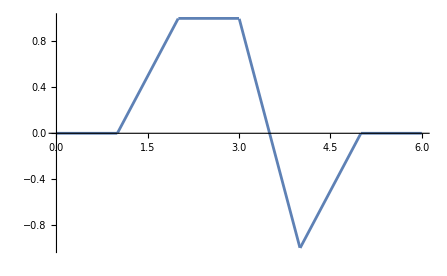

```mathematica
Plot[f[t1],{t1,tInit,tFinal}]
```

## Compute the Field-Dependent Quantities

First, we find the magnetizations/ fixed points as a function of the fields in a data-driven way.

```mathematica
mFinder[hx_,hy_]:=NSolve[{3 hx-mx^3+3 gPaper (-mx+my)==0,3 hy-my^3+3 gPaper (-my+mx)==0},{mx,my},Reals][[1,All,2]];
```

```mathematica
c={{1.3,-0.95},{-0.95,1.3}}*(0.025)^2;
mnd=MultinormalDistribution[{0,0},c];
Plot3D[Exp[-0.5*{x,y}.Inverse[c].{x,y}],{x,-0.1,0.1},{y,-0.1,0.1},PlotRange->Full]
```

-Graphics3D-

```mathematica
MTableMaker[hxMin_,hxMax_,hyMin_,hyMax_,nPts_]:=Module[{tx,ty,hTable,hTable2,hx,hy,mx,my},
tx={};
ty={};
hTable={};
Do[Do[AppendTo[hTable,{hxt,hyt}];
,{hxt,hxMin,hxMax,(hxMax-hxMin)/49}];
,{hyt,hyMin,hyMax,(hyMax-hyMin)/49}];
Join[hTable,RandomVariate[mnd,nPts]];
Do[{mx,my}=mFinder[N[hTable[[i,1]]],N[hTable[[i,2]]]];
AppendTo[tx,{hTable[[i]],mx}];
AppendTo[ty,{hTable[[i]],my}];
,{i,1,Length[hTable]}];
Return[{tx,ty}];
];
```

```mathematica
minhx=-0.1;
maxhx=0.1;
minhy=-0.1;
maxhy=0.1;
{tx,ty}=MTableMaker[minhx,maxhx,minhy,maxhy,1000];
```

```mathematica
mxFit=Interpolation[tx];
myFit=Interpolation[ty];
Plot3D[mxFit[hx,hy],{hx,-0.1,0.1},{hy,-0.1,0.1}]
```

-Graphics3D-

Using the fixed point, we implement the formula for the Jacobian/ linearized force.

```mathematica
JacobianMat[k1m_,hx_,hy_]:=-k1m*{{gPaper+mxFit[hx,hy]^2,-gPaper},{-gPaper,gPaper+myFit[hx,hy]^2}};
```

We implement the relevant propensities for the diffusion matrix. Note: compared to the notes, these are missing a factor of (k^-)_1 n_c, but this is a common factor that is multiplied in later.

```mathematica
Rx[hx_,hy_]:=((hx+1/3) +(mxFit[hx,hy]+1)+(mxFit[hx,hy]+1)^2 +(mxFit[hx,hy]+1)^3/3);
Ry[hx_,hy_]:=((hy+1/3) +(myFit[hx,hy]+1)+(myFit[hx,hy]+1)^2 +(myFit[hx,hy]+1)^3/3);
Dx[hx_,hy_]:=gPaper*(mxFit[hx,hy]+1);
Dy[hx_,hy_]:=gPaper*(myFit[hx,hy]+1);
```

We introduce the factor that was missing into the diffusion matrix.

```mathematica
DiffMatSchlogl[nc_,k1m_,hx_,hy_]:=k1m*nc*{{Rx[hx,hy]+Dx[hx,hy]+Dy[hx,hy],-Dx[hx,hy]-Dy[hx,hy]},{-Dx[hx,hy]-Dy[hx,hy],Ry[hx,hy]+Dx[hx,hy]+Dy[hx,hy]}};
DiffMatLandau[kbT_,k1m_]:=2*(k1m*kbT)*{{1,0},{0,1}};
```

## Solve for the Covariance Matrix

The steady state corresponding to the initial field is used as the initial condition for the covariance matrix in the dynamic case, so we provide methods to compute the steady state covariance matrix and mutual information.

```mathematica
GetSteadyStateCovariancesSchlogl[nc_,k1m_,hx_,hy_]:=Module[{c11,c12,c22},
Return[{{c11,c12},{c12,c22}}/.(NSolve[{JacobianMat[k1m,hx,hy].{{c11,c12},{c21,c22}} + {{c11,c12},{c21,c22}}.Transpose[JacobianMat[k1m,hx,hy]]==-DiffMatSchlogl[nc,k1m,hx,hy]},{c11,c12,c21,c22}][[1]])];
];
```

```mathematica
GetSteadyStateMISchlogl[nc_,k1m_,hx_,hy_]:=Module[{cov},
cov=GetSteadyStateCovariancesSchlogl[nc,k1m,hx,hy];
Return[-0.5*Log[1-cov[[1,2]]^2/(cov[[1,1]]*cov[[2,2]])]];
];
```

```mathematica
GetSteadyStateCovariancesLandau[nc_,k1m_,hx_,hy_]:=Module[{c11,c12,c22},
Return[{{c11,c12},{c12,c22}}/.(NSolve[{JacobianMat[k1m,hx,hy].{{c11,c12},{c21,c22}} + {{c11,c12},{c21,c22}}.Transpose[JacobianMat[k1m,hx,hy]]==-DiffMatLandau[nc,k1m]},{c11,c12,c21,c22}][[1]])];
];
```

```mathematica
GetSteadyStateMILandau[nc_,k1m_,hx_,hy_]:=Module[{cov},
cov=GetSteadyStateCovariancesLandau[nc,k1m,hx,hy];
Return[-0.5*Log[1-cov[[1,2]]^2/(cov[[1,1]]*cov[[2,2]])]];
];
```

## Steady State Mutual Information with the Same Local Field: Schlogl

Set the relevant parameters.

```mathematica
k1mPaper=1;
ncFig1=1000;
```

Compute the mutual information vs h_X = h_Y = h, plot, and write to file.

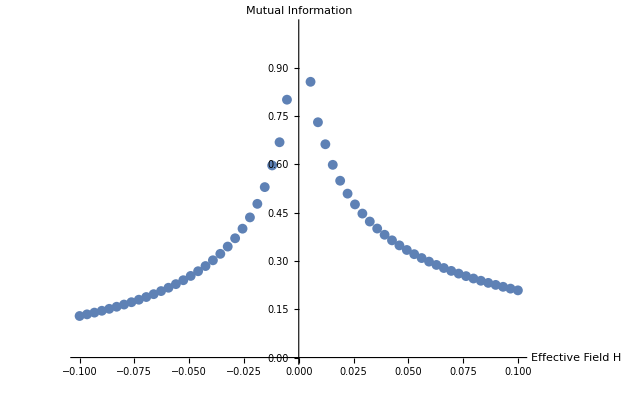

```mathematica
numSimPtsAboveCriticality=30;
negativehSimFig1=Array[#&,numSimPtsAboveCriticality,{-0.05,-0.001}];
positivehSimFig1=Array[#&,numSimPtsAboveCriticality,{0.001, 0.05}];
hSimFig1=Join[negativehSimFig1,positivehSimFig1];
MISchloglSamePtsFig1=Table[{hSimFig1[[i]]*2,GetSteadyStateMISchlogl[ncFig1,k1mPaper,hSimFig1[[i]],hSimFig1[[i]]]},{i,1,Length[hSimFig1]}];
ListPlot[MISchloglSamePtsFig1,AxesLabel->{"Effective Field H", "Mutual Information"}]
Export["Fig1_LNA_Schlogl_Same_Pts.csv",MISchloglSamePtsFig1,"CSV"];
```

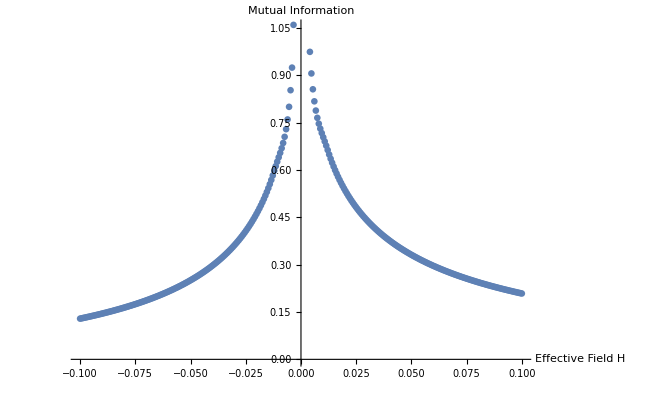

```mathematica
numPts=150;
negativehHighRes=Array[#&,numPts,{-0.05,-0.00001}];
positivehHighRes=Array[#&,numPts,{0.00001, 0.05}];
hHighRes=Join[negativehHighRes,positivehHighRes];
MISchloglHighResFig1=Table[{hHighRes[[i]]*2,GetSteadyStateMISchlogl[ncFig1,k1mPaper,hHighRes[[i]],hHighRes[[i]]]},{i,1,Length[hHighRes]}];
ListPlot[MISchloglHighResFig1,AxesLabel->{"Effective Field H", "Mutual Information"}]
Export["Fig1_LNA_Schlogl_High_res.csv",MISchloglHighResFig1,"CSV"];
```

## Steady State Mutual Information with the Same Local Field: Landau

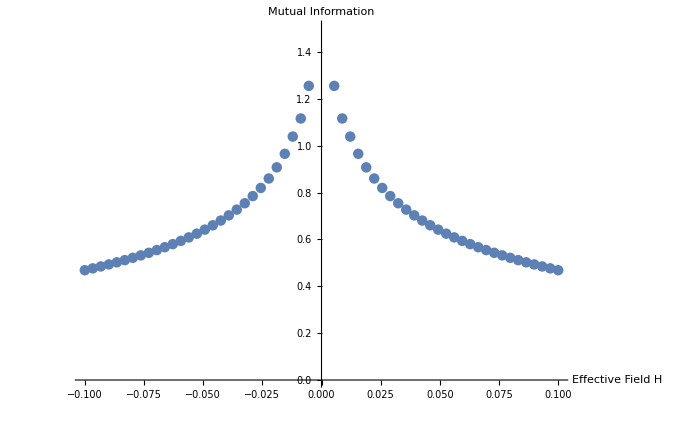

```mathematica
MILandauSamePtsFig1=Table[{hSimFig1[[i]]*2,GetSteadyStateMILandau[ncFig1,k1mPaper,hSimFig1[[i]],hSimFig1[[i]]]},{i,1,Length[hSimFig1]}];
ListPlot[MILandauSamePtsFig1,AxesLabel->{"Effective Field H", "Mutual Information"}]
Export["Fig1_LNA_Landau_Same_Pts.csv",MILandauSamePtsFig1,"CSV"];
```

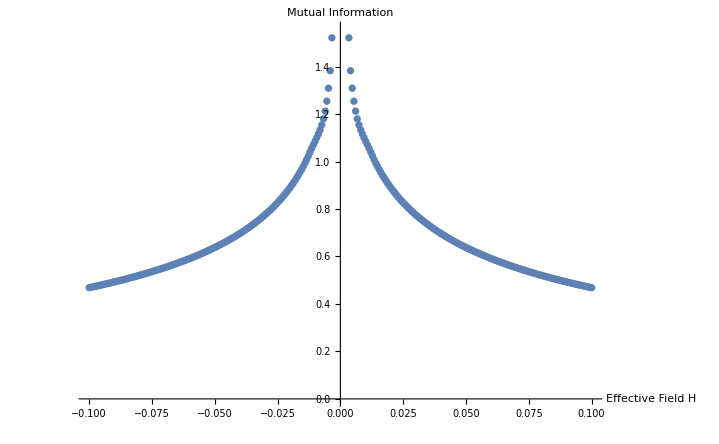

```mathematica
MILandauHighResFig1=Table[{hHighRes[[i]]*2,GetSteadyStateMILandau[ncFig1,k1mPaper,hHighRes[[i]],hHighRes[[i]]]},{i,1,Length[hHighRes]}];
ListPlot[MILandauHighResFig1,AxesLabel->{"Effective Field H", "Mutual Information"}]
Export["Fig1_LNA_Landau_High_res.csv",MILandauHighResFig1,"CSV"];
```